```mathematica
(* For Exporting *)
SetDirectory[NotebookDirectory[]];

bin=Databin["66W7CW2x"];

(* Take the arbitrary number stored and convert it to a DaetObject, then a string *)
times=Normal[DateString/@(DateObject/@Dataset[bin][All,"Timestamp"])];
(* Use the names from the last row to be sure to have them all *)
names=Select[Keys[Dataset[bin][Length[Dataset[bin]]]]//Normal,StringContainsQ[#,"("]&];
Clear[data]
data=ToExpression[names/.(Dataset[bin][All,names]//Normal)];
dayTimes=N[(AbsoluteTime[#]-AbsoluteTime[times[[Length[times]]]])/(3600*24)]&/@times;

(* This may not work when a new candidate is added now... *)
InvalidNum=-1;
data=Module[{emptyData},

emptyData=Table[Table[

If[Or[Length[data[[j]]]<i,
StringLength[ToString[data[[j,i]]]]==0],
InvalidNum,data[[j,i]]]

,{i,Length[names]}],{j,Length[data]}]];
(* This one will be better... *)
MissingIndices[name_String]:=Union[Flatten[Position[MissingQ/@Dataset[bin][All,name],True]]]

lastNamesWithParty=Module[{split},(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names];
lastNamesWithoutParty=Module[{split},(split=StringSplit[#];split[[2]])&/@names];

(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Differences[data];
percentDiffData=absoluteDiffData/data[[1;;Length[data]-1]]//N;
titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};
findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]

graphFn[option_Integer,selection_List,scale_Integer]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData]];
graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];

fn[ConvertToTimes[graph[[All,selection]],graphTimes],PlotLegends->labels[[selection]],
PlotLabel->plotLabel,
PlotRange->All]]

pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]

tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
(*NewCandidate[names,times,data,"like_data.csv"]*)



(* FIXME : Need a new replacement for the NewCandidate -- base it on the MissingIndices function? *)
```

```mathematica
Manipulate[
graphFn[option,selection,scale],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}}
]
```

```mathematica
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,If[option≤2,Length[times],Length[times]-1],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
CloudDeploy[%111,Permissions->"Public"]
```

CloudObject[]

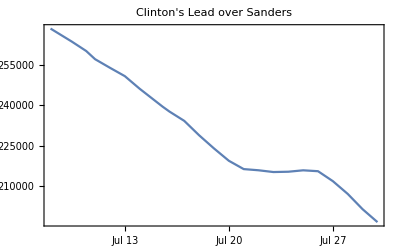

{{x→64.1535}}

```mathematica
DateListPlot[Table[{times[[i]],data[[i,findIndex["Clinton"]]]-data[[i,findIndex["Sanders"]]]},{i,6,Length[data]}],PlotLabel->"Clinton's Lead over Sanders"]
(* FIXME: Make this based on time, not index -- some days aren't at the same time*)
Solve[LinearModelFit[{dayTimes[[6;;]],data[[6;;,findIndex["Clinton"]]]-data[[6;;,findIndex["Sanders"]]]}//Transpose,{x},x]["BestFit"]==0,x]
```

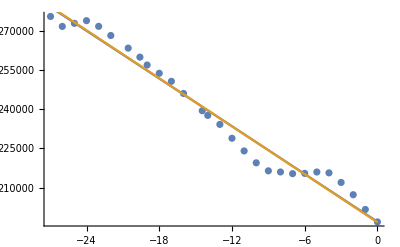

```mathematica
Show[ListPlot[{dayTimes,data[[All,findIndex["Clinton"]]]-data[[All,findIndex["Sanders"]]]}//Transpose],
Plot[{Normal[LinearModelFit[{dayTimes[[;;]],data[[;;,findIndex["Clinton"]]]-data[[;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t},
Normal[LinearModelFit[{dayTimes[[6;;]],data[[6;;,findIndex["Clinton"]]]-data[[6;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t}},{t,-Length[data],0}]
]
```

```mathematica
((#[[1]])/#[[2]]//N)&/@percentDiffData[[All,{findIndex["Sanders"],findIndex["Clinton"]}]]
```

{2.81561,1.13268,1.13681,1.97213,2.59463,2.65418,2.68433,3.00363,2.82221,2.65728,2.80926,2.05777,2.16439,2.45424,2.96975,3.38932,3.09057,2.3433,1.37053,1.49049,1.20241,1.04448,1.37509,2.89527,3.94649,3.52474,3.21272}

```mathematica
Manipulate[Labeled[TableForm[Sort[{#,(LinearModelFit[{dayTimes[[;;]],data[[;;,findIndex[#]]]}//Transpose,{x},x]["BestFit"]/.{x->time})}&/@lastNamesWithoutParty,#1[[2]]>#2[[2]]&]],
"Estimated Total Likes from Linear Fit\n"<>DatePlus[times[[Length[times]]],time]
,Top],{time,1,478,1}]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{-29.9688, -29.0001, -28.0001, -27.0001, -26.0001, -24.9973, -23.5621, « 17 », -5.99992, -5., -3.99993, -3.00001, -1.99997, -1.00006, 0.}, {}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Transpose::nmtx: The first two levels of {{-29.9688, -29.0001, -28.0001, -27.0001, -26.0001, -24.9973, -23.5621, « 17 », -5.99992, -5., -3.99993, -3.00001, -1.99997, -1.00006, 0.}, {}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{-29.9688, -29.0001, -28.0001, -27.0001, -26.0001, -24.9973, -23.5621, « 17 », -5.99992, -5., -3.99993, -3.00001, -1.99997, -1.00006, 0.}, {}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

```mathematica
(*SetDirectory[NotebookDirectory[]];
data2=Import["like_data.csv"];
bin=Databin["66W7CW2x"];
names=data2[[1]];
data2=data2[[2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data2[[j]]]<i,
StringLength[ToString[data2[[j,i]]]]==0],
InvalidNum,data2[[j,i]]]

,{i,Length[names]}],{j,Length[data2]}];
data2=emptyData;

(* Add literally everything *)
For[i=1,i≤Length[data2],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[i,1;;Length[names]]]}]]]]
(*  THIS IS THE IMPORTANT ONE -- HOW TO ADD IN CASE OF ERROR   *)
data2=Import["like_data.csv"];
names=data2[[1]];
DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[Length[data2],1;;Length[names]]]}]]]


times=(DateObject/@Dataset[bin][All,"Timestamp"]);*)
(*ResetTheDatabin[]:=For[i=0,i<Length[data],i++,DatabinRemove[bin,1]]*)
(*For[i=1,i≤Length[data],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data[[i]]}]]]]*)
```

```mathematica
DatabinRemove[bin,32]
```

Databin[…]

```mathematica
Differences[data]/data[[1;;Length[data]-1]]//N
```

{{0.00250509,0.00207086,0.0000658222,0.00307593,0.0012941,0.0297851,0.0177518,0.00289163,0.000270525,-0.0000114186,0.000935529,0.0043266,0.000934181,0.000626268,0.000774748,0.010375,0.00262452,0.00795389,0.,0.00368481,0.000248223},{0.00274949,0.00160432,0.0000801782,0.00430678,0.00138535,0.0122477,0.0177932,0.00250721,0.000438232,0.0000418687,0.000804973,0.00227706,0.000672532,0.000502281,0.000519785,0.00765408,0.00283105,0.00672538,0.,0.00675748,0.000223},{0.00121523,0.00132122,0.0000478637,0.00374322,0.00188113,0.00843416,0.0173048,0.00137552,0.000275339,-0.0000114183,0.000514358,0.00184207,0.000452625,0.00031814,0.000418928,0.00674197,0.00276631,0.0064881,0.,0.00593063,0.000150442},{0.000902631,0.00119295,-5.98268×10^-6,0.00239829,0.00207125,0.00902802,0.0183569,0.0024975,0.000265254,0.000156051,0.000805492,0.00864182,0.000808873,0.000405443,0.000730331,0.0096049,0.00841751,0.00690445,0.,0.00487033,0.000264343},{0.00146209,0.000640898,0.000041879,0.00227647,0.00196614,0.00573243,0.0171984,0.00149477,0.000291035,0.000114166,0.000834828,0.0109376,0.000684932,0.000461646,0.000580747,0.00992291,0.00435366,0.00846723,0.,0.0038244,0.000190316},{0.00161707,0.00108251,0.0000287158,0.00251803,0.00249897,0.00781792,0.0211626,0.00211443,0.000371816,0.00018645,0.00109036,0.0149666,0.00158795,0.000775815,0.000826477,0.0130537,0.0043441,0.0130649,0.,0.00491818,0.000285913},{0.000964084,0.000630784,0.000276382,0.00175531,0.00189883,0.00324812,0.0130315,0.00136527,0.000297509,0.000140763,0.000745018,0.00769869,0.00131208,0.000509491,0.000541342,0.00906199,0.00356039,0.0118524,0.,0.00337588,0.000270554},{0.000993732,0.000729447,0.0000693754,0.00202555,0.00139429,0.0025139,0.0100796,0.00148736,0.000253266,0.000524932,0.000940416,0.000881523,0.000559635,0.000500228,0.000557578,0.00704582,0.00251761,0.00825539,0.,0.00234577,0.000204955},{0.000714013,0.000548936,0.0000107644,0.00207481,0.00141736,0.00421733,0.0116257,0.00123762,0.000290682,0.000311753,0.000911229,0.000704597,0.000627532,0.000550032,0.00053414,0.00772101,0.00211962,0.0121727,0.,0.0027358,0.000230034},{0.000595222,0.000557629,0.0000239206,0.00170199,0.00214801,0.0173281,0.0127926,0.00197775,0.000145715,0.0000532095,0.000520004,0.000528076,0.000558971,0.000472723,0.000394062,0.00783425,0.00224848,0.0152163,0.,0.00294823,0.000160544},{0.000922808,0.00105171,0.0000442521,0.00142318,0.00142063,0.00606196,0.00798393,0.00333087,0.000182325,0.000167221,0.000540931,0.00170068,0.000899305,0.000766336,0.000422514,0.0111133,0.00235355,0.013645,0.,0.00395595,0.000287061},{0.0018363,0.00387917,0.000141122,0.003982,0.00282064,0.00687565,0.016838,0.00209025,0.000585166,0.000212791,0.00149951,0.00163925,0.00269549,0.000706803,0.00113173,0.0227542,0.00432988,0.0277941,0.00279345,0.0110577,0.000603985},{0.000490556,0.00708433,0.0000597891,0.00202676,0.0011499,0.00341435,0.0047811,0.00147239,0.000263712,0.0000113971,0.00075059,0.00116898,0.000773889,0.000191863,0.000450422,0.00544989,0.00135352,0.0069037,0.000724699,0.00251797,0.000152012},{0.00080579,0.00411234,0.0000669598,0.00391016,0.00178484,0.00424426,0.0091435,0.00159275,0.00038174,0.0000341909,0.00116184,0.000525425,0.000963221,0.000619229,0.000722547,0.00885437,0.00247127,0.011884,0.00114102,0.00360778,0.000238067},{0.0012305,0.0011057,-0.0000119563,0.00446181,0.00193838,0.00542864,0.012036,0.00244648,0.000323399,0.000053184,0.00125511,0.000991948,0.00203302,0.000526355,0.000723122,0.0113048,0.00236984,0.0155085,0.00146081,0.00380666,0.000187851},{0.00234418,0.000918923,0.000131521,0.00380591,0.00262616,0.00416727,0.00988306,0.00231849,0.000240186,0.000296295,0.00106375,0.000699505,0.00228588,0.000372009,0.000723696,0.00929247,0.00264052,0.0249444,0.00123318,0.00274169,0.000190274},{0.000980132,0.000776836,0.000109985,0.00280349,0.00211021,0.00465519,0.00822382,0.00170441,0.000283334,0.000163294,0.000966655,0.00104852,0.00238863,0.000277223,0.000490881,0.00911224,0.00185208,0.018572,0.000823457,0.0029484,0.000171066},{0.000582211,0.000564533,0.0000406421,0.00267652,0.00195828,0.00463362,0.00705558,0.0013369,0.000267472,0.000201236,0.00105692,0.000989235,0.00148092,0.000381285,0.000531162,0.00777163,0.00168633,0.0113418,0.0011322,0.00331653,0.000183816},{0.00102017,0.000643557,0.0000872574,0.00300545,0.0056998,0.00336086,0.0128784,0.00254885,0.000351274,0.000208788,0.00143888,0.00267411,0.00151906,0.00115965,0.000853786,0.00587192,0.00231368,0.0159677,0.00148916,0.00428441,0.000721861},{0.000811526,0.00119819,0.0000310753,0.00245581,0.00467548,0.00367031,0.0122508,0.00338983,0.000722225,0.000201154,0.00121211,0.00301484,0.000630864,0.001449,0.00124021,0.00465068,0.00220056,0.0127215,0.00130809,0.00312023,0.000250922},{0.00218746,0.000448782,0.,0.00272553,0.0025899,0.00671022,0.00643046,0.00180985,0.000231443,0.00018973,0.0014739,0.00300578,0.000764608,0.00129842,0.000859647,0.00346495,0.00148772,0.0104166,0.00139745,0.00288168,0.000249877},{0.00260793,0.000527742,0.0000968084,0.00232354,0.00216344,0.00655969,0.00617744,0.00240877,0.000156748,0.0000569081,0.00224714,0.00201706,0.000831043,0.0011083,0.000770508,0.00308577,0.00168238,0.0086655,0.00140599,0.00295437,0.000153619},{0.00269123,0.000351642,0.0000274862,0.00185994,0.00194128,0.00276795,0.00459489,0.00204253,0.00018077,0.0000796668,0.0016781,0.00109277,0.000642854,0.000990687,0.000706664,0.00404298,0.00123286,0.0068645,0.00132019,0.00294016,0.000146725},{0.00153853,0.000369094,0.0000167302,0.00180932,0.00215458,0.00296995,0.00570763,0.0028777,0.000174105,0.0000872471,0.00151231,0.00132138,0.000762899,0.000589707,0.000630971,0.00735152,0.00128042,0.00636296,0.00133589,0.00253915,0.000171236},{0.00151,0.000553437,0.0000657248,0.00208342,0.00251095,0.00358823,0.00754382,0.00502152,0.000192311,0.000299649,0.00193574,0.00275403,0.00115016,0.00114147,0.000730768,0.00775936,0.00217438,0.00776773,0.00122264,0.00196614,0.000190339},{0.00076506,0.00121162,0.0000250933,0.0021725,0.00172045,0.00159678,0.00781687,0.00368784,0.00016824,0.0000796296,0.00185502,0.00211707,0.00162975,0.00112239,0.000563728,0.00973451,0.00240975,0.0081971,0.00128029,0.00276176,0.000236897},{0.000727183,0.000798001,0.0000286773,0.00213576,0.0015817,0.00187149,0.00664603,0.00260756,0.00010275,-0.0000568738,0.00153889,0.000970652,0.000933582,0.000420495,0.000680878,0.00856244,0.00166769,0.0104056,0.000809584,0.00266517,0.000232428},{0.000674485,0.000753553,0.0000442096,0.00212836,0.00192216,0.000795628,0.00930647,0.00260078,0.0000820259,0.0000985868,0.00170299,0.001369,0.000932712,0.000202396,0.000848888,0.0055735,0.0022494,0.00676059,0.00090614,0.00187832,0.00016227},{0.000402184,0.000499072,0.0000501817,0.00169053,0.00147268,0.00134803,0.00662361,0.00129702,0.0000231973,0.000113743,0.00140679,0.000968385,0.000612354,0.000197366,0.000495217,0.00368813,0.00205438,0.00534437,0.000849821,0.00226892,0.000308802},{0.000215901,0.000236285,0.000193548,0.00259035,0.00162154,0.00296859,0.00546477,0.00188413,0.0000231968,-0.0000568649,0.00120522,0.000625996,0.000824841,0.000140235,0.000369058,0.00564563,0.0016754,0.00434445,0.00050946,0.00224214,0.000375838}}